## 1) Towards a Theory of Bulk Orchestration

#### Objective:

Develop a foundational theoretical framework that allows one to greatly simplify accurate molecular-scale (and larger) simulations in biology

#### Background:

In chemistry, one can do molecular dynamics to simulate the behavior of every single molecule in a system.  But for many chemical purposes, it’s sufficient to use what amounts to a probabilistic model in which all that matters is the overall concentration of molecules of different types.  For biology this approach is often tried, but is much less likely to work, because biological systems don’t consist of randomly mixed molecules.  Instead, a major takeaway from molecular biology over the past few decades has been that there’s some kind of “bulk orchestration” of molecular processes: molecules are not moving around randomly, but are carefully channeled through a network of interactions, associated with particular membranes, enzymes, etc.  

Currently, there is no bulk way to analyze or simulate systems like this, or characterize on a large scale what they are doing.  The goal here is to develop such a theory.  

The approach will be to design highly idealized computer simulations that attempt to get to the heart of the problem.  Among the things identified so far are what Stephen Wolfram calls the “mechanoidal phase”, minimal models for biological evolution, and actual data on the engineering structures made in the Game of Life cellular automaton.

The expectation is that biological life fundamentally makes use of certain “pockets of computational reducibility” that can be thought as associated with bulk orchestration.  If one can identify these, then one can effectively reduce them out for purposes of simulation, thereby dramatically increasing efficiency.  

Part of this project can potentially be done with very simple idealizations (such as cellular automata).  Another part to be explored has to do more realistically with the behavior of large molecules.  Once one no longer makes independent probabilistic model of interactions, one is dealing with what one can call “subchemistry”, in which one has to track individual molecules, and the causal relationships between their interactions. The formalism for things like this has been developed to some extent in the Wolfram Physics Project.  Here we would develop it further, and see how it informs bulk orchestration with actual molecules.

```mathematica
sts2 = ResourceFunction["WolframModel"][{{1,2,3},{4,2,5}}->{{6,3,1},{3,6,4},{1,2,6}},{{0,0,0},{0,0,0}},1000, "StatesList"];
```

```mathematica
GraphicsColumn[
{
GraphicsRow[(ArrayPlot[#,
ColorRules->{0->White,
1->{{"[◼]", "SecondLawColors"}}["Reds",3],
2->{{"[◼]", "SecondLawColors"}}["Reds",1]
},
FrameStyle->GrayLevel[0.7],
ImageSize->{100, Automatic}]&@(Take[First[#],{180,220}]&/@ResourceFunction["BlockCellularAutomaton"][{{
{1,0}->{0,1},{0,1}->{1,0},{1,2}->{0,2},
{2,1}->{2,0},{2,0}->{1,2},{0,2}->{2,1},
{1,1}->{2,2},{0,0}->{0,0},{2,2}->{1,1}},2},
{CenterArray[#,400],0},100]))&/@Table[
Table[2,x],{x,1,11,2}],ImageSize->{725, Automatic},Spacings->15],GraphicsRow[ResourceFunction["WolframModelPlot"][#, ImageSize -> 15Length[#]^.4]&/@ sts2[[Table[Round[2.35^i], {i,1, 8}]-1]],(* Frame->True, FrameStyle->Directive[Thickness[.0025],GrayLevel[.7]],*) Spacings->{20, 30}]}, Frame->All, FrameStyle->Directive[Thickness[.0025],GrayLevel[.7]]]
```

-Graphics-

Figure 1.  Two examples of systems where each of the parts is following simple rules, but global structure still emerges. On the top is a block cellular automata from different initial conditions. [3] The subpatterns within the automata have some obvious structure. On the bottom is a hypergraph rewriting system, where each frame is a stage in the evolution. [4] The hypergraph produced by this rewrite rule converges to a smooth geometric surface.

```mathematica
DevonAndScottMonoterpenes=CloudGet[CloudObject[["https://www.wolframcloud.com/obj/rnachbar/DevonAndScottMonoterpenes"](https://www.wolframcloud.com/obj/rnachbar/DevonAndScottMonoterpenes)]];
geranylCationTEGwithEvents=CloudGet[CloudObject[["https://www.wolframcloud.com/obj/rnachbar/geranylCationTEGwithEvents"](https://www.wolframcloud.com/obj/rnachbar/geranylCationTEGwithEvents)]];
geranylCation=Molecule["[CH2+]C=C(C)CCC=C(C)C"];
carbonSkeleton[molIn_Molecule] := carbonSkeleton[molIn] = 
	Module[{mol, atoms, bonds, p, b}, 
		atoms = AtomList[molIn]; 
		bonds = BondList[molIn]; 
		(* take only carbon atoms, discared all properties *)
		p = First /@ Position[atoms, Atom["C", ___], {1}]; 
		atoms = atoms[[p]] /. Atom[a_, ___] :> Atom[a]; 
		(* take only bonds between carbon atoms, set type to single and renumber *)
		b = Thread[p -> Range@Length[p]]; 
		bonds = Select[bonds, AllTrue[First@#, MemberQ[p, #]&]&] /. Bond[idx_, ___] :> Bond[idx /. b, "Single"]; 
		mol = Molecule[atoms, bonds]; 
		(* take the largest fragment *)
		ConnectedMoleculeComponents[mol] // TakeLargestBy[AtomCount, 1] // First
		]
sameSkeletonQ[mols__Molecule] := sameSkeletonQ[mols] = 
	carbonSkeleton /@ {mols} // AllTrue[Partition[#, 2, 1], Apply[MoleculeMatchQ]]&
sameSkeletonQ[] := False
Options[tokenGraph]={
"untagEdges"->False
};
tokenGraph[g_Graph,opts:OptionsPattern[{tokenGraph,Graph}]]:=
Module[{v,e,gOpts=Association@Options@g},
v=Cases[VertexList@g,_Molecule];
e=Join@@(Cases[EdgeList@g,DirectedEdge[#⟦2⟧,token_,tag_]:>DirectedEdge[#⟦1⟧,token,tag]]&)/@Cases[EdgeList@g,DirectedEdge[_Molecule,__]];
If[TrueQ@OptionValue["untagEdges"],
e=e/.DirectedEdge[a_,b_,_]:>DirectedEdge[a,b]//DeleteDuplicates
];
gOpts[VertexLabels]=DeleteCases[gOpts[VertexLabels],{"Event",__}->_];
gOpts[VertexStyle]=DeleteCases[gOpts[VertexLabels],{"Event",__}->_];
Graph[v,e,Sequence@@FilterRules[{opts},Options[Graph]],Sequence@@Normal@gOpts]
]
Module[{geranylCationTEGwithoutEvents,targets},
geranylCationTEGwithoutEvents=tokenGraph@geranylCationTEGwithEvents;
targets=Cases[VertexList[geranylCationTEGwithoutEvents],m_Molecule/;AnyTrue[DevonAndScottMonoterpenes,sameSkeletonQ[#,m]&]];
VertexDelete[geranylCationTEGwithoutEvents,Complement[VertexList[geranylCationTEGwithoutEvents],FindShortestPath[geranylCationTEGwithoutEvents, geranylCation, #] & /@ targets//Apply[Union]],GraphLayout->"LayeredDigraphEmbedding",ImageSize->24 72,AspectRatio->1/2]
]//Rasterize[#,ImageSize->9 72]&
```

-Graphics-

Figure 2. This is a partial token-event graph of monoterpene biosynthesis starting from geraniol out to six steps and illustrates how you can track individual molecule interactions over time.

Another direction relates to the origin of bulk orchestration, which it may well be necessary to understand.  How do interactions between molecules build up things like autocatalytic sets that are relevant to the fundamental characteristics of life?  For this, we have methods based on multiway systems and other idealizations, together with idealized and not-so-idealized chemistry.  Early simulations show considerable promise, but have to be developed further, possibly using fairly large-scale computation.

## 2) Highly Idealized Models for Host-Pathogen Interactions and Evolution

#### Objective:

Develop foundational models that give strategic intuition about the space of possible viral threats, and support the development of practical strategies for threat neutralization and attribution

#### Background:

Stephen Wolfram recently developed highly minimal models that (for the first time) seem to capture core features of biological evolution at the phenotypic level, i.e. with representations of the space of phenotypes and the way that different phenotypic structures can be produced.

```mathematica
SeedRandom[1111];
rand=RandomSample[{{"[◼]", "allperts"}}[CellularAutomaton[{299459058088077823758143088095350287424,4,1},{{1},0},{102,{-200,200}}],4],400];Magnify[Module[{ru={299459058088077823758143088095350287424,4,1}},FeatureSpacePlot[With[{pca={{"[◼]", "PerturbedCellularAutomaton"}}[ru,{{1},0},{102,{-200,200}},#,"ReturnPerturbations"->False]},Rasterize[{{"[◼]", "PlotCA"}}[pca]]->{{"[◼]", "PlotCA"}}[pca,"Trim"->{3,None}]]&/@rand,LabelingSize->100,PlotStyle->AbsolutePointSize[9],Frame->True,FrameTicks->None,FrameStyle->Gray,RandomSeeding->64453,PerformanceGoal->"Static",ImageSize->2000]],.31]
```

Figure 3. The resulting patterns of making small perturbations to a cellular automaton, arranged according to their morphological features. There is some clustering, but no obvious categories that emerge, an effect we expect to hold for variation between real biological systems.

Figure 4.  A graph representing all possible paths evolution can take. One can see different, somewhat discrete branches or “hubs”, much like the discrete branches and common ancestors in the tree of life.The evolution here is purely mutational, with the fitness function being the length of the pattern. For this project, we would draw this graph for more virus-like evolutionary algorithms, and different fitness functions.

These studies were done using particular sets of fitness functions.  The objective here would be to consider a much wider range of fitness functions, that idealize fitness functions encountered in viral etc. binding in biological systems.  Specifically, the initial approach would consist of investigating by enumerative simulation how easy or not it is to optimize different fitness functions.  

In SW’s original model, there is pure mutation.  We would want to generalize that to allow lateral gene transfer of the type seen in viruses, to find out how it affects what fitness functions can readily be evolved to.

We can think of the “viral” evolution as being evolution of a “key”.  We also need to study evolution of the “lock”, i.e. the organism (human, crop, etc.) into which the key is binding.  In other words, we want to study what fitness functions will be relevant.

Part of what will come out of this is an understanding of what structures can easily be “naturally evolved”, and what intermediates should occur in that evolution, versus what structures are more likely to have been produced by explicit engineering.

The basic studies envisaged here are idealized and computational.  But we anticipate that it will be possible to make contact with actual data on viruses, their binding sites, etc. This can then be further developed into a computational system that can be used for general simulation of the evolutionary paths of viruses.

## 3) Minimal models for classification and attribution of adaptive systems

#### Objective

Construct minimal, yet universal, theoretical methodologies that lets one look at an arbitrary adaptive system and tell, in some quantitative way, whether it is the product of unguided evolution or purposeful engineering.

#### Background

The Game of Life offers a multi-decade long “closed‑world” record of engineering innovation: thousands of patterns whose origins are known, from discovered (automated search), adapted (evolutionary algorithms) and invented (constructed by humans). Analysis of the two regimes shows differences in their multiway causal graphs. Engineered objects show shallow causal depth, obvious modular reuse and pockets of computational reducibility; search‑generated objects reach further into the computational wilderness, and find whole patterns with little to no reusable parts.

If you lay out the possible patterns in a casual graph, you can slice the space with reference frames based on a computational observer’s sophistication, such as causal graph depth or space-like boundedness, and could reveal qualitatively different feature spaces that can be found. We can apply the same analytic lens to viral genomes, and even begin to record what could be signatures of specific engineering approaches; which distinguish random evolutionary drift from purposeful construction, and also could reveal methods for attribution of design.

```mathematica
Row[Framed[#,FrameStyle->Opacity[.3]]&/@{{{"[◼]", "PatternsLayeredGraph"}}[{{"[◼]", "Data"}}["$LifeData"]["Period-15 glider gun"],Automatic,"VertexSizeFunction":>(6 Sqrt[Dimensions[#]]&)],{{"[◼]", "BoundingBoxLayeredGraph"}}[{{"[◼]", "Data"}}["$LifeData"]["Period-15 glider gun"]]},Spacer[20]]
```

```mathematica
Framed[{{"[◼]", "PatternsLayeredGraph"}}[{{"[◼]", "Data"}}["$LifeData"]["Period-15 glider gun"],Automatic,"VertexSizeFunction":>(6 Sqrt[Dimensions[#]]&)],FrameStyle->Opacity[.3]]
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

Figure 5. A graph showing the progression of an “engineered” cellular automaton in the Game of Life. Each node represents a causally independent part in the system. At each timestep, there are many modular parts that work together to achieve some objective, in this case to produce a small sub-pattern that moves across the array of cells, or a “glider” in Game of Life terms.

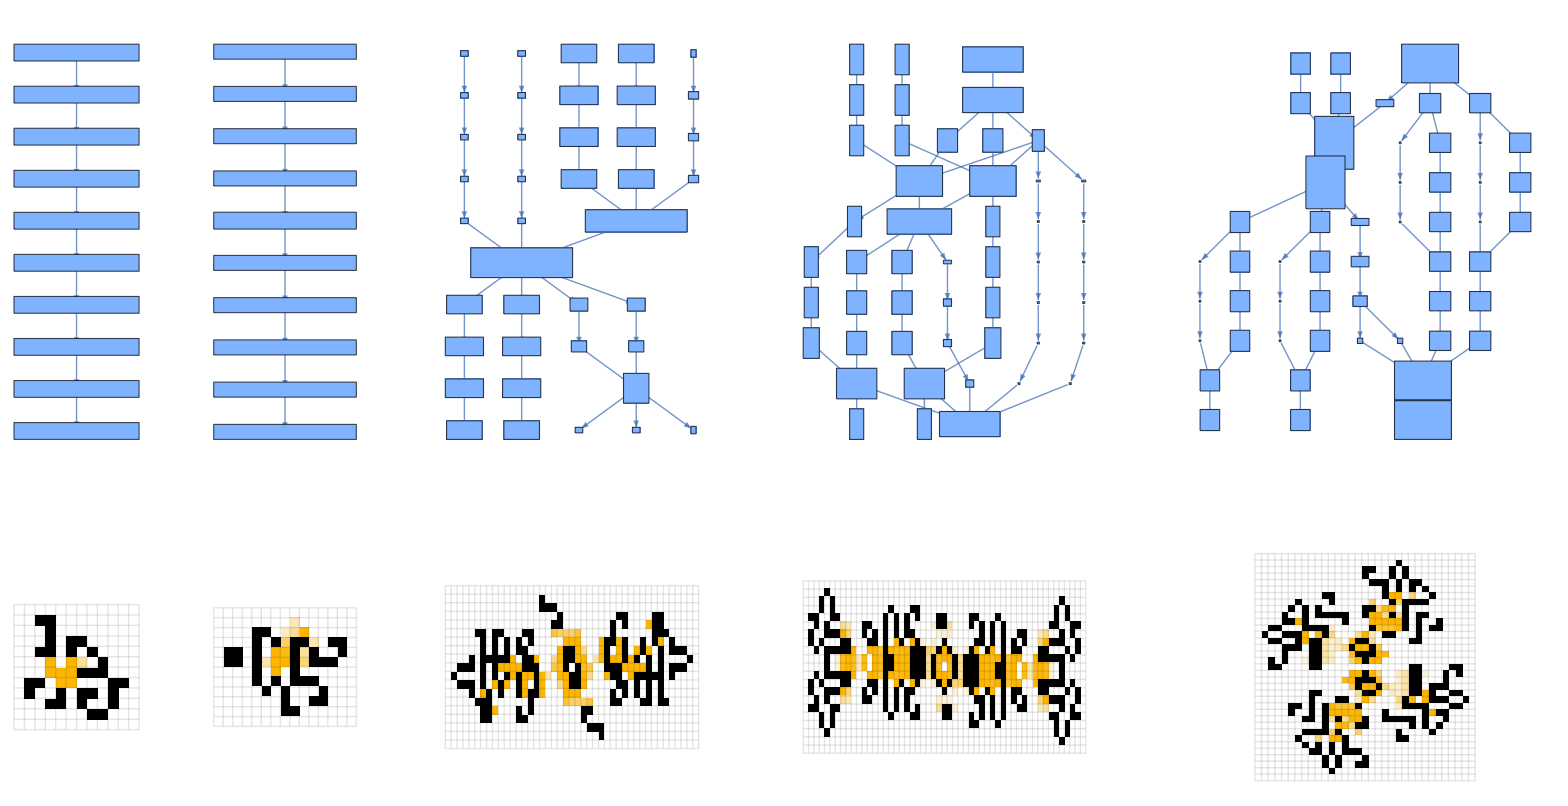

```mathematica
vertfunc = Function[{pos,val,blah},Rectangle[pos-#/45,pos+#/45]&@(Subtract@@(Reverse@MinMax[#])&/@Transpose[Ramp[val[[-1]]]])];
Style[Row[With[{elems=With[{data=Select[ResourceData["LifeWiki Dataset 2025"],#Class === "Oscillator" && #Period ==9&]},MapIndexed[{Graph[{{"[◼]", "BoundingBoxLayeredGraph"}}[#, Automatic, VertexShapeFunction->vertfunc],ImageSize->{Automatic,130}],{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{#MatrixData,0},9,ImageSize->13Sqrt[Reverse@Dimensions[#1["MatrixData"]]]]}&,Values[SortBy[data//Quiet,#Year&]][[{4, 5, 9, 10, 11}]]]]},GraphicsGrid[Transpose[#],Dividers->{All,False}, Spacings->12, FrameStyle->GrayLevel[.3]]&/@Partition[elems, UpTo[6]]]],LineSpacing->{1,40}]
```

Figure 6.  Discovered and invented cellular automata from the Game of Life, with the first two panels being found by automated computer search and the others being constructed by explicit human effort. The causal graphs of the patterns found by search are less modular, indicated by a fewer number of causally independent nodes at each step in the graph.

The approach would need to take into account the potential for threat actors to want to hide their tracks and make an engineered gene appear of natural origin. So we would want to pinpoint these features that an engineer cannot alter without destroying function, or alternatively models of identifying permanent residual markers.

Similar to red-teaming exercises in software security, we can create adversarial scenarios to study the theoretical ability to both conceal and attribute features of these adaptive systems.

## References

3.

4. Stephen Wolfram (2020), “A Class of Models with the Potential to Represent Fundamental Physics”, https://www.wolframphysics.org/technical-introduction/limiting-behavior-and-emergent-geometry/

[1] Stephen Wolfram (2024), “Foundations of Biological Evolution: More Results & More Surprises,” Stephen Wolfram Writings. https://writings.stephenwolfram.com/2024/12/foundations-of-biological-evolution-more-results-more-surprises/#distribution-in-morphospace.

[2] Stephen Wolfram (2024), “Foundations of Biological Evolution: More Results & More Surprises,” Stephen Wolfram Writings. https://writings.stephenwolfram.com/2024/12/foundations-of-biological-evolution-more-results-more-surprises/#the-multiway-graph-of-all-possible-evolutions.